```mathematica
ClearAll[Phi,PPi,Dx];
Phi[t_,x_]=A*Cos[2*π*omega*t] Sin[2*π*kx*x];
PPi[t_,x_]=Derivative[1,0][Phi][t,x];
Dx[t_,x_]=Derivative[0,1][Phi][t,x];

ClearAll[PhiRhs,PPiRhs,DxRhs];
PhiRhs[t_,x_]=Pi[t,x];
PPiRhs[t_,x_]=Derivative[0,1][Dx][t,x];
DxRhs[t_,x_]=Derivative[0,1][Pi][t,x];
```

```mathematica
StringReplace[ToString[Phi[t,x],FortranForm],{"Pi"->"pi","Cos"->"cos","Sin"->"sin"}]
StringReplace[ToString[PPi[t,x],FortranForm],{"Pi"->"pi","Cos"->"cos","Sin"->"sin"}]
StringReplace[ToString[Dx[t,x],FortranForm],{"Pi"->"pi","Cos"->"cos","Sin"->"sin"}]
```

A*cos(2*omega*pi*t)*sin(2*kx*pi*x)

-2*A*omega*pi*sin(2*omega*pi*t)*sin(2*kx*pi*x)

2*A*kx*pi*cos(2*omega*pi*t)*cos(2*kx*pi*x)

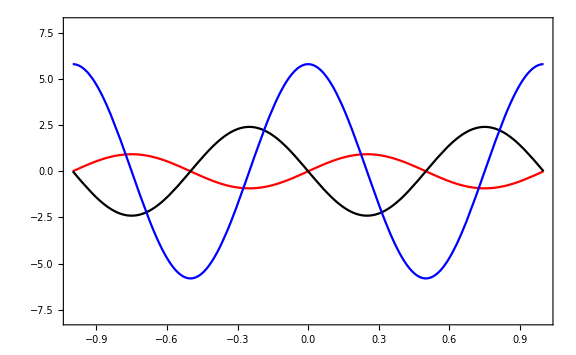

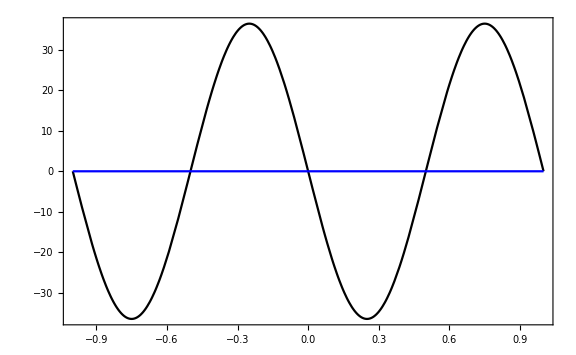

```mathematica
ClearAll[t,A,omega,kx];
A=1;
kx=1;
omega=Sqrt[kx^2];
t=10*625*10^-5;

Plot[
{
Phi[t,x],
PPi[t,x],
Dx[t,x]
},
{x,-1,1},
PlotStyle->{Red,Black,Blue},
Axes->False,
Frame->True,
PlotRange->{{-1,1},{-8,8}},
ImageSize->Large
]

Plot[
{
PhiRhs[t,x],
PPiRhs[t,x],
DxRhs[t,x]
},
{x,-1,1},
PlotStyle->{Red,Black,Blue},
Axes->False,
Frame->True,
PlotRange->{{-1,1},Full},
ImageSize->Large
]
ClearAll[t,A,omega,kx];
```